```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\nivu1\OneDrive - ETHZ\Dokumente\Stanford\bais loop bispectrum\Final_code\EFTBispectrum

```mathematica
LaunchKernels[16]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

### Compiled J ( Not tested for Abs[Im[ν]]>10 )

```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
GammaC=Compile[{{z,_Complex}},
Block[{q0,q1,q2,q3,q4,q5,q6,p1,p2,result},
q0=75122.6331530+0.0I;
	q1=80916.6278952+0.0I;
	q2=36308.2951477+0.0I;
	q3=8687.24529705+0.0I;
	q4=1168.92649479+0.0I;
	q5=83.8676043424+0.0I;
	q6=2.50662827511+0.0I;
If[Re[z]≥0,p1=(q0+q1 z+q2 z^2+q3 z^3+q4 z^4+q5 z^5+q6 z^6)/(z(z+1)(z+2)(z+3)(z+4)(z+5)(z+6));result=p1 (z+5.5)^(z+0.5)Exp[-z-5.5],p1=(q0+q1(1-z)+q2 (1-z)^2+q3 (1-z)^3+q4 (1-z)^4+q5 (1-z)^5+q6 (1-z)^6)/((1-z)(2-z)(3-z)(4-z)(5-z)(6-z)(7-z));p2=p1(1-z+5.5)^(1-z+0.5)Exp[-1+z-5.5];result=π/(Sin[π z]p2)];
result
],
{{Sin[_],_Complex},{Exp[_],_Complex},{Re[_],_Real}}, 
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
Hyp2F1basic=Compile[{{a,_Complex},{b,_Complex},{c,_Complex},{z,_Complex}},
Block[{p,s,sold,eps,n},
s=0.0+0.0 I;
p=1.0+0.0I;
eps=1.0;
n=0.0;
While[eps>10^-12,
sold=s;
s=s+p;
p=p((a+n)(b+n))/((c+n)(n+1))z;
eps=Abs[(s-sold)/s];
n++];
s
],
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
JFastC = Compile[{{ν1,_Complex},{ν2,_Complex},{ν3,_Complex},{x,_Complex},{y,_Complex},{epscr,_Real}},
Block[
{p1,p2,s1,s2,s1old,s2old,eps,n,result},
s1=0.+I 0.;
p1=(GammaC[2-2 ν2] GammaC[2-2 ν3] Sin[π ν2] Sin[π ν3])/GammaC[5-2 ν2-2 ν3] x^(1.5-ν2-ν3);
p2=(GammaC[2-2 ν1] GammaC[2 (-2+ν1+ν2+ν3)] Sin[π ν1] Sin[π (ν1+ν2+ν3)])/GammaC[-1+2 ν2+2 ν3] y^(1.5-ν1-ν3);
s2=0.+I 0.;
eps=1.;
n=0.0;
While[eps>epscr,
s1old=s1;
s2old=s2;

s1=s1+p1 Hyp2F1basic[ν1+n,1.5-ν2+n,3-ν2-ν3+2 n,1-y];
s2=s2+p2 Hyp2F1basic[ν2+n,1.5-ν1+n,ν2+ν3+2 n,1-y];

p1=p1*((n+ν1) (3-ν1-ν2-ν3+n) (1.5-ν3+n) (1.5-ν2+n))/((1+n) (2.5-ν2-ν3+n) (4-ν2-ν3+2 n) (3-ν2-ν3+2 n)) x;
p2=p2*((1.5-ν1+n) (ν1+ν2+ν3-1.5+n) (n+ν2) (n+ν3))/((1+n) (ν2+ν3-0.5+n) (1+ν2+ν3+2 n) (ν2+ν3+2 n)) x;

eps=Abs[(s1-s2-s1old+s2old)/(s1-s2)];
n++];

result=Sec[π (ν2+ν3)]/(2 π^2) (s1-s2);
result
],
{{GammaC[_],_Complex},{Sec[_],_Complex},{Abs[_],_Real},{Sin[_],_Complex}}
,
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
JFastCa[arr_,x_,y_]:= JFastC[10^-10+arr[[1]],10^-10+arr[[2]],10^-10+arr[[3]],x,y,10^-8];
```

#### J function numerical check

```mathematica
NIntegrate[q^2/(2π)^3/((q^2)^(0.9+3I)(1+q^2-2 q μ)^(0.6+I)(q^2+y+q (-1+x-y) μ+q √(-x^2-(-1+y)^2+2 x (1+y)) √(1-μ^2) Cos[ϕ])^(1+1.3I))/.{x->0.3,y->0.8},{ϕ,0,2π},{μ,-1,1},{q,0,1000},MaxPoints->1000000,AccuracyGoal->10]//Quiet//AbsoluteTiming
```

{5.48983,0.0176001+0.00370646 ⅈ}

```mathematica
ν1=0.9+3I;
ν2=0.6+I;
ν3=1+1.3I;
x=0.3;
y=0.8;
res=(Gamma[3/2-ν3]Gamma[ν1+ν2+ν3-3/2])/(4 π^2 Gamma[ν1]Gamma[ν2])NIntegrate[u^(ν1-1)(1-u)^(ν2-1)(x(1-u)+y u)^(3/2-ν1-ν2-ν3)Hypergeometric2F1[1.5-ν3,-1.5+ν1+ν2+ν3,1.5,1-(u(1-u))/(x(1-u)+y u)],{u,0,1}]//AbsoluteTiming
Clear[ν1,ν2,ν3,x,y];
```

{0.277959,0.0176001+0.00370646 ⅈ}

```mathematica
JFastC[0.9+3I,0.6+I,1+1.3I,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.0015103,0.0176001+0.00370646 ⅈ}

```mathematica
NIntegrate[q^2/(2π)^3/((q^2)^0.9(1+q^2-2 q μ)^(0.6+I)(q^2+y+q (-1+x-y) μ+q √(-x^2-(-1+y)^2+2 x (1+y)) √(1-μ^2) Cos[ϕ])^1)/.{x->0.3,y->0.8},{ϕ,0,2π},{μ,-1,1},{q,0,1000},MaxPoints->1000000,AccuracyGoal->10]//Quiet//AbsoluteTiming
```

{10.2678,0.0617987+0.0555097 ⅈ}

```mathematica
JFastC[0.9,0.6+I,0.9999999,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.0001521,0.0617986+0.0555097 ⅈ}

```mathematica
JFastC[0.99999,0.9,0,0.1,0.2,10^-8]//AbsoluteTiming
```

{0.0000866,0.129282+0. ⅈ}

```mathematica
JFastC[0.9,0.6+I,0 0.9999999,0.3,0.8,10^-8]//AbsoluteTiming
```

{0.0000805,0.0245486-0.0135016 ⅈ}

```mathematica
J2[1,0.9,0.6+I]
```

J2[1,0.9,0.6+1. ⅈ]

### Linear PS and decomposition

```mathematica
plindat=Import["PlinPlanck_z0p56.dat"];
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^0.965},{i,1,30}];
plindat2=Join[pextra,plindat];
plinus=Interpolation[plindat2];
plinint=Interpolation[Log[plindat2]];
```

```mathematica
khigh=40.;
pcut[k_]= Exp[plinint[Log[k]]]Exp[-(k/khigh)];
plin[k_]=pcut[k];
```

```mathematica
(* Nmax log k bins, form kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
(* A table of coefficents and powers in FFTLog decomposition of the linear power spectrum *)
CoeffPow[b_,Nmax_,k0_,kmax_,Plin_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

```mathematica
bias=-0.2501//N;
Nmax=26;
kmin=10^-3;
kmax=1;
cn=CoeffPow[bias,Nmax,kmin,kmax,plin];
kn=kBins[Nmax,kmin,kmax];
khigh=40.;
```

```mathematica
P11[dat_,ns_]:=Module[{plindat,As,kb,pextra,plindat2,plinus,plinint,pcut,plin},
plindat=dat;
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^ns},{i,1,30}];
plindat2=Join[pextra,plindat];
plinus=Interpolation[plindat2];
plinint=Interpolation[Log[plindat2]];
pcut[k_]= Exp[plinint[Log[k]]]Exp[-(k/khigh)];
plin[k_]:=pcut[k];
plin]
```

```mathematica
cns[dat_,ns_]:=Module[{plindat,As,kb,pextra,plindat2,plinus,plinint,pcut,plin},
plindat=dat;
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^ns},{i,1,30}];
plindat2=Join[pextra,plindat];
plinus=Interpolation[plindat2];
plinint=Interpolation[Log[plindat2]];
pcut[k_]= Exp[plinint[Log[k]]]Exp[-(k/khigh)];
plin[k_]=pcut[k];
CoeffPow[bias,Nmax,kmin,kmax,plin]]
```

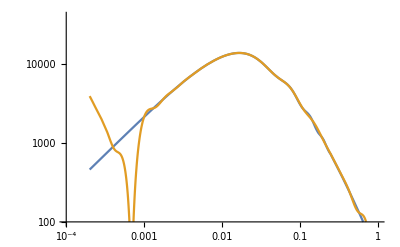

```mathematica
LogLogPlot[{plin[k],Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]]},{k,2 10^-4,1},PlotRange->{{10^-4,1},{100,40000}}]
```

### Tree Level Kernels

#### Petrubation Theory Kernels

```mathematica
perm12=Permutations[{q1,q2}];
```

```mathematica
Clear[Fn,Gn,n,m];
Fn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
test[n_,v_]:=Sum[be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]],{m,1,n-1}]
```

```mathematica
F2[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
G2[q1_,q2_]=Simplify[Sum[1/Length[perm12]Gn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+1/2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
```

#### Compute Redshift space kernels

define (c̃)_i parameters and (ĉ)_i kernels (see Appendix A)

initialize values

```mathematica
adelta = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
btheta = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
adelta[[1]]="((c̃)^A)_(δ, 1)";
adelta[[2]]="((c̃)^A)_(δ, 2 (2))";
adelta[[3]]="((c̃)^A)_(δ, 2 (3))";
adelta[[4]]="((c̃)^A)_(δ, 3)";
adelta[[5]]="((c̃)^A)_(δ, 3 SubscriptBox[c, s])";
adelta[[6]]="((c̃)^A)_(δ^2)";
adelta[[7]]="((c̃)^A)_(δ^2)";
adelta[[8]]="((c̃)^A)_(δ^2)";
adelta[[9]]="((c̃)^A)_(s^2)";
adelta[[10]]="((c̃)^A)_(δ^3)";

btheta[[1]]="((c̃)^B)_(δ, 1)";
btheta[[2]]="((c̃)^B)_(δ, 2 (2))";
btheta[[3]]="((c̃)^B)_(δ, 2 (3))";
btheta[[4]]="((c̃)^B)_(δ, 3)";
btheta[[5]]="((c̃)^B)_(δ, 3 SubscriptBox[c, s])";
btheta[[6]]="((c̃)^B)_(δ^2)";
btheta[[7]]="((c̃)^B)_(δ^2)";
btheta[[8]]="((c̃)^B)_(δ^2)";
btheta[[9]]="((c̃)^B)_(s^2)";
btheta[[10]]="((c̃)^B)_(δ^3)";
```

```mathematica
c1 = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
c2 = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
c3 = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
c4 = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
c4[[1]]=Subscript["(ĉ)^(4)","δ,1"];
c4[[2]]=Subscript["(ĉ)^(4)","δ,2"];
c4[[3]]=Subscript["(ĉ)^(4)","δ,3"];
c4[[4]]=Subscript["(ĉ)^(4)","δ,4"];
c4[[5]]=Subscript["(ĉ)^(4)","δ^2,1"];
c4[[6]]=Subscript["(ĉ)^(4)","δ^2,2"];
c4[[7]]=Subscript["(ĉ)^(4)","δ^2,3"];
c4[[8]]=Subscript["(ĉ)^(4)","r^2,2"];
c4[[9]]=Subscript["(ĉ)^(4)","r^2,3"];
c4[[10]]=Subscript["(ĉ)^(4)","δ^3,1"];
c4[[11]]=Subscript["(ĉ)^(4)","δ^3,2"];
c4[[12]]=Subscript["(ĉ)^(4)","r^3,2"];
c4[[13]]=Subscript["(ĉ)^(4)","r^2δ,2"];
c4[[14]]=Subscript["(ĉ)^(4)","δ^4,1"];
c4[[15]]=Subscript["(ĉ)^(4)","δr^3,1"];
```

```mathematica
c3=c4//.{"(ĉ)^(4)"-> "(ĉ)^(3)"};
c2=c4//.{"(ĉ)^(4)"-> "(ĉ)^(2)"};
c1=c4//.{"(ĉ)^(4)"-> "(ĉ)^(1)"};
adelta = c4//.{"(ĉ)^(4)"-> "(c̃)^A"};
```

```mathematica
btheta={1,2,3,4,-1,-3/2,-2,0,0,1,4/3,0,0,-1,0};
```

```mathematica
biasA={0,0,0,0,0};
biasB={0,0,0,0,0};
biasA[[1]]="(b^A)_(δ, 1)";
biasA[[2]]="(b^A)_(δ, 2)";
biasA[[3]]="(b^A)_(δ, 3)";
biasA[[4]]="(b^A)_(δ^2)";
biasA[[5]]="(b^A)_c_s";

biasB[[1]]="(b^B)_(δ, 1)";
biasB[[2]]="(b^B)_(δ, 2)";
biasB[[3]]="(b^B)_(δ, 3)";
biasB[[4]]="(b^B)_(δ^2)";
biasB[[5]]="(b^B)_c_s";
```

expressions for ĉ kernels

```mathematica
c3[[{1,2,3,5,6,8,10}]];
```

```mathematica
For[i=1,i<16,i++,c1[[i]][q1_]:=0;]
For[i=1,i<16,i++,c2[[i]][q1_,q2_]:=0;]
For[i=1,i<16,i++,c3[[i]][q1_,q2_,q3_]:=0;]
```

```mathematica
c1[[1]][q1_]:=1;
c2[[1]][q1_,q2_]:=-(mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)/(2 mag[q1]^2);
c2[[2]][q1_,q2_]:=((1+2 F2[q1,q2]) mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)/(2 mag[q1]^2);
c2[[5]][q1_,q2_]:=1;
c3[[1]][q1_,q2_,q3_]:=1/8 (-(2 G2[q2,q3] (2 mag[q1]^2+mag[q2]^2-mag[q1+q2]^2+mag[q3]^2-mag[q1+q3]^2))/mag[q2+q3]^2+1/(mag[q2]^2 mag[q3]^2)(mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q2]^2+2 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2));
c3[[2]][q1_,q2_,q3_]:=-1/(4 mag[q2]^2 mag[q3]^2)(mag[q1]^2+(1+2 F2[q1,q2]) mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q2]^2+2 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2);
```

##### halo kernels in redshift space (see Appendices B and C)

vector substitutions for k, q, and z-hat

```mathematica
k12sub={k1->{0,0,kk1},k2->kk2{0,√(1-y^2), y}};
kq123sub=Join[k12sub,{k3->-k1-k2/.k12sub//Simplify},{q->{qq √(1-x^2) α,qq √(1-x^2) √(1-α^2),qq x}}(*/.{α->Cos[ϕ]}/.{x->Cos[β]}*)]//Simplify//PowerExpand;
(*kqsub={k-> kk{0,0,1},q-> {qq √(1-x^2) α,qq √(1-x^2) √(1-α^2),qq x}}//Simplify;*)
```

```mathematica
kmq[k1] = √(k1^2+q^2-2 k1 q x);
kmq[k2] = √(k2^2+q^2-2 k2 q (x y+√(1-x^2) √(1-y^2) √(1-α^2)));
kmq[k3] = √(k3^2+q^2+2k1 q x+2k2 q x y+2k2 q √(1-x^2) √(1-y^2) √(1-α^2));
kpq[k1] = √(k1^2+q^2+2 k1 q x);
kpq[k2] = √(k2^2+q^2+2 k2 q (x y+√(1-x^2) √(1-y^2) √(1-α^2)));
kpq[k3] = √(k3^2+q^2-2k1 q x-2k2 q x y-2k2 q √(1-x^2) √(1-y^2) √(1-α^2));
```

```mathematica
yrep = {y->(-k1^2-k2^2+k3^2)/(2 k1 k2)};
```

```mathematica
magreps ={mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k3]->k3,mag[-k1]->k1,mag[-k2]->k2,mag[-k1-k2]->k3,mag[k1+k2]->k3,mag[-k1+q]->k1mq,mag[k1-q]->k1mq,mag[-k1-q]->k1pq,mag[k1+q]->k1pq,mag[-k2+q]->k2mq,mag[k2-q]->k2mq,mag[-k2-q]->k2pq,mag[k2+q]->k2pq,mag[-k1-k2-q]->k3mq,mag[k1+k2+q]->k3mq,mag[-k1-k2+q]->k3pq,mag[k1+k2-q]->k3pq,mag[-k3]->k3,mag[-k1-k3]->k2,mag[k1+k3]->k2,mag[-k3+q]->k3mq,mag[k3-q]->k3mq,mag[-k3-q]->k3pq,mag[k3+q]->k3pq,mag[-k1-k3-q]->k2mq,mag[k1+k3+q]->k2mq,mag[-k1-k3+q]->k2pq,mag[k1+k3-q]->k2pq,mag[-k2-k3]->k1,mag[k2+k3]->k1,mag[-k2-k3-q]->k1mq,mag[k2+k3+q]->k1mq,mag[-k2-k3+q]->k1pq,mag[k2+k3-q]->k1pq};
```

```mathematica
magrevreps  = {k1mq-> √(k1^2+q^2-2 k1 q x),k1pq-> √(k1^2+q^2+2 k1 q x),k2mq-> √(k2^2+q^2-2 k2 q (x y+√(1-x^2) √(1-y^2) √(1-α^2))),k2pq-> √(k2^2+q^2+2 k2 q (x y+√(1-x^2) √(1-y^2) √(1-α^2))),k3mq-> √(k3^2+q^2+2k1 q x+2k2 q x y+2k2 q √(1-x^2) √(1-y^2) √(1-α^2)),k3pq-> √(k3^2+q^2-2k1 q x-2k2 q x y-2k2 q √(1-x^2) √(1-y^2) √(1-α^2))};
```

```mathematica
(*zhat = {Sin[ω]Cos[γ],Sin[ω]Sin[γ], Cos[ω]};*)
(*μrep = {Sin[ω]-> √(1-μ^2),Cos[ω]-> μ}(*μ=cos[ω],ν=Cos[γ]*)*)
```

```mathematica
(*zhatinμ = {√((-1+y^2+μ1^2-2 y μ1 μ2+μ2^2)/(-1+y^2)),(-y μ1+μ2)/(√(1-y^2)),μ1}*)
μ0rep =x μ1+(√(1-x^2) √(1-α^2) (-y μ1+μ2))/(√(1-y^2))+√(1-x^2) α √((-1+y^2+μ1^2-2 y μ1 μ2+μ2^2)/(-1+y^2))
```

x μ1+(√(1-x^2) √(1-α^2) (-y μ1+μ2))/(√(1-y^2))+√(1-x^2) α √((-1+y^2+μ1^2-2 y μ1 μ2+μ2^2)/(-1+y^2))

```mathematica
kzsub = {Subscript[k1, z]-> k1*μ1,Subscript[k2, z]-> k2*μ2,Subscript[q, z]-> q*μ0,Subscript[k3, z]-> -Subscript[k1, z]- Subscript[k2, z]};
```

```mathematica
zμsub = {μ1->  Cos[ω],μ2-> (y Cos[ω]+√(1-y^2) Sin[γ] Sin[ω]), μ0->  (x Cos[ω]+√(1-x^2) (α Cos[γ]+√(1-α^2) Sin[γ]) Sin[ω])};
```

```mathematica
zμsub2 = {μ1->  μ,μ2-> (y μ+√(1-y^2) √(1-μ^2) √(1-ν^2)), μ0->  (x μ+√(1-x^2) √(1-μ^2) (α ν+√(1-α^2) √(1-ν^2)))};
```

define symmetrization over two and three variables

```mathematica
q2sym[f_,q1_,q2_]:=1/2(f[q1,q2]+f[q2,q1]);
q3sym[f_,q1_,q2_,q3_]:=Total[(f@@@Permutations[{q1,q2,q3}])/(3!)];
q4sym[f_,q1_,q2_,q3_,q4_]:=Total[(f@@@Permutations[{q1,q2,q3,q4}])/(4!)]
```

```mathematica
biases = {b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15};
tb=Thread[adelta-> biases];
```

Halo Kernels

```mathematica
K1[aa_]:=aa[[1]];
K2[q1_,q2_,aa_]:=K2[q1,q2,aa]=((Table[c2[[i]][q1,q2],{i,1,15}]/.{al->alfm,be->befm}/.{mag[-q]->mag[q]}/.magreps//Expand)/.mag[0]-> 0//Simplify).aa;
```

First-order redshift-space halo kernels

```mathematica
K1r[q1_]:=K1[adelta]+f1 kz^2/((q1).(q1))K1[btheta]//.{kz-> q1.zhat}//.Dot[a_,a_]-> mag[a]^2/.{Dot[a_,zhat]-> Subscript[a, z]}/.magreps//.kzsub;
```

Second-order redshift-space halo kernels

```mathematica
K2r[q1_,q2_]:=K2[q1,q2,adelta]+f1   kz^2/((q1+q2).(q1+q2))K2[q1,q2,btheta]+ f1 kz 1/2((q1.zhat)/(q1.q1)+(q2.zhat)/(q2.q2))K1[btheta]K1[adelta]+1/2 f1^2 kz^2((q1.zhat)(q2.zhat))/((q1.q1)(q2.q2))K1[btheta]K1[btheta]/.{al->alfm,be->befm}/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
```

```mathematica
K2rsym[q1_,q2_]:=q2sym[K2r,q1,q2];
```

### 1-Loop Powespectrum

#### Preliminaries

```mathematica
NmaxPlot=400;
kminPlot=10^-3;
kmaxPlot=4;
knPlot=kBins[NmaxPlot,kminPlot,kmaxPlot];
```

```mathematica
J2[k_,ν1_,ν2_]:=1/(2π)^3(Gamma[3/2-ν1]Gamma[3/2-ν2]Gamma[ν1+ν2-3/2])/(Gamma[ν1]Gamma[ν2]Gamma[3-ν1-ν2])π^(3/2)k^(3-2ν1-2ν2);
```

#### Tree-Level

```mathematica
PTree[k_]:=K1r[k]^2 Plin[k]/.tb/.magreps;
```

#### P13

```mathematica
P13ab=((b1+f1 μ^2) (-8 (b3+15 b8)+9 b1 (1+n1) (1+2 f1 μ^2)+3 f1 μ^2 (-5-6 f1+3 n1+6 f1 n1 μ^2)) Tan[n1 π])/(112 (-3+n1) (-2+n1) (-1+n1) n1 (1+n1) π);
```

```mathematica
P13coefs = CoefficientList[(n1(-3+n1) (-2+n1) (-1+n1) (1+n1) π)/Tan[n1 π] P13ab//Expand//Simplify,n1]//Simplify;
```

```mathematica
P13list =  {Tan[n1 π]/(n1(-3+n1) (-2+n1) (-1+n1) (1+n1) π),Tan[n1 π]/((-3+n1) (-2+n1) (-1+n1) (1+n1) π)};
```

```mathematica
p13matrix[cn_]:= Monitor[Table[ParallelTable[ P13list[[i]]/.n1-> -0.5cn⟦j,2⟧,{j,1,Nmax+1}],{i,1,Length[P13list]}],i];
p13[cn_,plin_]:=Module[{p13mat},p13mat = p13matrix[cn]; Monitor[Table[ParallelTable[{knPlot⟦i⟧,knPlot⟦i⟧^3 plin[knPlot⟦i⟧]Re[p13mat[[j]].(knPlot⟦i⟧^cn⟦All,2⟧cn⟦All,1⟧)]},{i,1,NmaxPlot}],{j,1,Length[P13list]}],j]];
```

```mathematica
p13n[cn_,plin_]:= Module[{pp13,tab},pp13 =p13[cn,plin]; Table[(pp13[[i]]//Interpolation)[k],{i,1,Length[P13list]}]];
```

```mathematica
P13[cn_,plin_]:=p13n[cn,plin].P13coefs
```

#### P22

```mathematica
P22ab=(Gamma[3/2-n1] Gamma[3/2-n2] Gamma[-3/2+n1+n2])/(8 π^(3/2) Gamma[n1] Gamma[3-n1-n2] Gamma[n2])1/(1568 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2))(3136 b5^2 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)+64 b2^2 (-1+2 n1) (-1+2 n2) (48-2 n1 (1+10 n1)-2 n2+3 n1 (17+7 n1) n2+(-20+7 n1 (3+7 n1)) n2^2)+112 b5 f1 (1+n1) (-1+2 n1) (1+n2) (-1+2 n2) (-3+2 n1+2 n2) (-7 f1+2 (-8+7 n1+7 n2)) μ^2+f1^2 (-3+2 n1+2 n2) (-1+2 n1+2 n2) (147 f1^2 (-1+2 n1) (-1+2 n2)-28 f1 (-1+2 n1) (-1+2 n2) (-2+7 n1+7 n2)+784 b5 (-1+n1+2 n1^2) (-1+n2+2 n2^2)+8 (50-n1 (9+35 n1)-9 n2+2 n1 (-33+7 n1 (-9+7 n1)) n2+7 (-5+2 n1 (-9+14 n1)) n2^2+98 n1 n2^3)) μ^4+14 f1^3 (-3+2 n1+2 n2) (-1+2 n1+2 n2) (7 f1 (1+2 n1+2 n2) (1+2 (n1^2-4 n1 n2+n2^2))+2 (26+56 n1^3 n2+(9-38 n2) n2+2 n1^2 (-19+2 n2 (-9+28 n2))+n1 (9+4 n2 (-21+n2 (-9+14 n2))))) μ^6+49 f1^4 (-1+2 n1) (-1+2 n2) (-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (3+2 n1+2 n2) μ^8+196 b1^2 (2 (6+n1 (1+2 n1) (-7+n1+2 n1^2)-7 n2+2 n1 (-3+n1 (19+n1 (-5+4 (-3+n1) n1))) n2+(-13+2 n1 (19+6 n1-4 n1^2)) n2^2+2 (2+n1 (-5-4 n1+8 n1^2)) n2^3+4 (1-6 n1) n2^4+8 n1 n2^5)+f1 (-3+2 n1+2 n2) ((-1+n1+2 n1^2) (8-4 n1+f1 (2+n1 (-3+2 n1)))+(4 (1+2 n1) (3+2 (-2+n1) n1 (1+n1))+f1 (5-2 n1 (1+2 n1))) n2-(-12+f1+4 (10+f1) n1+8 (2+f1) n1^2-16 n1^3) n2^2-4 (2+f1+2 n1-4 n1^2) n2^3+4 (f1+4 n1) n2^4) μ^2+f1^2 (-1+2 n1) (1+n1+n2) (2+n1+n2) (-1+2 n2) (-3+2 n1+2 n2) (-1+2 n1+2 n2) μ^4)+16 b2 (-1+2 n1) (-1+2 n2) (56 b5 (1+n1) (1+n2) (3-2 n2+n1 (-2+7 n2))+f1 (-3+2 n1+2 n2) μ^2 (-7 f1 (9+3 n1+3 n2+7 n1 n2)+2 (-58+n1 (4+35 n1)+4 n2+7 n1 (2+7 n1) n2+7 (5+7 n1) n2^2)+7 f1 (-1+2 n1+2 n2) (5+5 n1+5 n2+7 n1 n2) μ^2))+28 b1 (56 b5 (1+n1) (-1+2 n1) (1+n2) (-1+2 n2) (n1 (-3+2 n1)+n2 (-3+2 n2))+f1 (-3+2 n1+2 n2) (-7 f1 (-1+2 n1) (-1+2 n2) (n1 (-1+2 n1)+(-2+n2) (3+2 n2))+4 (28 n1^4 n2+n1^2 (5+14 b5 (1+n2) (-1+2 n2) (1+2 n2)+2 n2 (-19+14 (-1+n2) n2))-(-1+2 n2) (10+n2 (-3-n2+14 b5 (1+n2)))+n1^3 (2-46 n2+28 (n2^2+b5 (-1+n2+2 n2^2)))+n1 (-23+14 b5 (-1+n2) (1+n2) (-1+2 n2)+2 n2 (47+n2 (-19+n2 (-23+14 n2)))))) μ^2+f1^2 (-3+2 n1+2 n2) (-1+2 n1+2 n2) (38+112 n1^3 n2+(41-66 n2) n2+7 f1 (2+n1+4 n1^3+n2-8 n1^2 n2+4 n2^3-8 n1 n2 (1+n2))+2 n1^2 (-33+2 n2 (-9+28 n2))+n1 (41+4 n2 (-58+n2 (-9+28 n2)))) μ^4+7 f1^3 (-1+2 n1) (2+n1+n2) (-1+2 n2) (-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) μ^6+8 b2 (-1+2 n1) (-1+2 n2) (-18-12 n1+n1^2+10 n1^3-12 n2-38 n1 n2-11 n1^2 n2+14 n1^3 n2+n2^2-11 n1 n2^2+10 n2^3+14 n1 n2^3+f1 (-3+2 n1+2 n2) (2+n2 (4+5 n2)+n1^2 (5+7 n2)+n1 (4+n2 (10+7 n2))) μ^2)));
```

```mathematica
P22simp =(8 π^(3/2) Gamma[n1] Gamma[3-n1-n2] Gamma[n2] n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)P22ab)/(Gamma[3/2-n1] Gamma[3/2-n2] Gamma[-3/2+n1+n2])//Expand;
```

```mathematica
nlist = Join[Table[n2^i,{i,0,5}],n1 Table[n2^i,{i,0,5}],n1^2 Table[n2^i,{i,0,4}],n1^3 Table[n2^i,{i,0,3}],n1^4 Table[n2^i,{i,0,2}],n1^5 Table[n2^i,{i,0,1}]];
nlistno1 = Delete[nlist,1];
```

```mathematica
P22Coefs = Join[{P22simp},Coefficient[P22simp,nlistno1]]/.n1-> 0/.n2-> 0//Simplify;
P22list=nlist (Gamma[3/2-n1] Gamma[3/2-n2] Gamma[-3/2+n1+n2])/(8 π^(3/2) Gamma[n1] Gamma[3-n1-n2] Gamma[n2] n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2));
```

```mathematica
p22matrixbasic[cn_]:=Monitor[Table[ParallelTable[P22list[[s1]]/.n1-> -0.5cn⟦j1,2⟧/.n2-> -0.5cn⟦j2,2⟧,{j1,1,Nmax/2+1},{j2,1,Nmax+1}],{s1,1,Length[P22list]}],s1];
p22matrix[cn_]:=Module[{p22matbas},p22matbas =p22matrixbasic[cn]; Monitor[Table[Table[If[j1≤Nmax/2+1,p22matbas⟦j,j1,j2⟧,Conjugate[p22matbas⟦j,Nmax+2-j1,Nmax+2-j2⟧]],{j1,1,Nmax+1},{j2,1,Nmax+1}],{j,1,Length[P22list]}],j]];
p22[cn_]:=Module[{p22mat,p22plot,cnc},p22mat=p22matrix[cn];
p22plot=Table[Table[{0},{i,1,NmaxPlot}],{j,1,Length[P22list]}];
For[i=1,i≤Length[p22plot[[1]]],i++,
cnc=knPlot⟦i⟧^(1.5+cn⟦All,2⟧)cn⟦All,1⟧;
For[j=1,j≤Length[P22list],j++,p22plot⟦j,i⟧={knPlot⟦i⟧,Re[p22mat[[j]].cnc.cnc]}]];
p22plot];
p22n [cn_]:= Module[{pp22},pp22=p22[cn]; Table[(pp22[[i]]//Interpolation)[k],{i,1,Length[P22list]}]];
```

```mathematica
P22[cn_]:=p22n[cn].P22Coefs
```

#### Full Loop

```mathematica
P1loop[cn_,plin_]:=P13[cn,plin]+P22[cn];
```

```mathematica
Ploopexample[k_]=P1loop[cn,plin];
```

```mathematica
Ploopexample[0.1]/.f1-> 0//Simplify
```

0.+2366.71 b1^2+2950.35 b2^2+3294.06 b2 b5+381.24 b5^2+b1 (-5116.64 b2+217.013 b3-2371.68 b5+3255.2 b8)

#### Counter terms

```mathematica
StochasticP22[k_,μ_]:=1/nbar(ctP22[1]+k^2/kM^2 ctP22[2]+f1 k^2/kM^2 μ^2 ctP22[3])
```

```mathematica
CounterP13[k_,μ_]:=K1r[k]Plin[k](ctP13[1] k^2/kM^2+ ctP13[2]f1 k^2/kM^2 μ^2+ctP13[3] f1^2 k^2/kM^2 μ^4 )/.tb/.magreps;
```

```mathematica
FullPcounter[k_,μ_]:=2CounterP13[k,μ]+StochasticP22[k,μ]
```

### 1-Loop Bispectrum

#### Preliminaries

```mathematica
μ3rep=μ3->(-k1 μ1-k2 μ2)/k3;
```

```mathematica
CtabB411=<<"tables/CtabB411.m";//AbsoluteTiming
CtabB3212=<<"tables/CtabB3212.m";//AbsoluteTiming
CtabB3211=<<"tables/CtabB3211.m";//AbsoluteTiming
CtabB222temp=<<"tables/Ctab222.m";//AbsoluteTiming
```

{2.17947,Null}

{0.0403406,Null}

{34.2566,Null}

{0.491972,Null}

Angular substitutions for B222

```mathematica
B222μ1=<<"tables/CtabB222mu1.m";
B222μ2=<<"tables/CtabB222mu2.m";
B222μ3=<<"tables/CtabB222mu3.m";
```

```mathematica
TJμ4=<<"tables/CtabTdotint4.m";
TJμ5=<<"tables/CtabTdotint5.m";
TJμ6=<<"tables/CtabTdotint6.m";

TTμ4=<<"tables/TdotT4.m";
TTμ5=<<"tables/TdotT5.m";
TTμ6=<<"tables/TdotT6.m";

Tzμ4=<<"tables/Tdotz4.m";
Tzμ5=<<"tables/Tdotz5.m";
Tzμ6=<<"tables/Tdotz6.m";
```

Preliminaries for permutations of tabs

```mathematica
biases = {b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15};
```

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list⟦#⟧&];
```

```mathematica
compressor[tab_] := Module[{tab1,tab2},
tab1 = positionDuplicates[Table[Delete[tab⟦i⟧,4],{i,1,Length[tab]}]];
tab2 = Monitor[Table[{tab⟦tab1⟦j,1⟧⟧⟦{1,2,3}⟧,
Sum[tab⟦tab1⟦j,i⟧⟧⟦4⟧,{i,1,Length[tab1⟦j⟧]}]}//Flatten,{j,1,Length[tab1]}],j*100.0/Length[tab1]]]
```

```mathematica
comp[tab_]:=Table[compressor[tab⟦i⟧],{i,1,Length[tab]}]
```

```mathematica
ksort[k1_,k2_,k3_]  := Sort[{k1,k2,k3}];
```

```mathematica
xv[k1_,k2_,k3_]:=(ksort[k1,k2,k3] [[1]])^2/(ksort[k1,k2,k3] [[3]])^2;
yv[k1_,k2_,k3_]:=(ksort[k1,k2,k3] [[2]])^2/(ksort[k1,k2,k3] [[3]])^2;
```

```mathematica
perms[k1_,k2_,k3_]:= Permutations[{{ksort[k1,k2,k3] [[3]],μ1t},{ksort[k1,k2,k3] [[2]],μ2t},{ksort[k1,k2,k3] [[1]],μ3t}}]/.{{a_,b_},{c_,d_},{e_,f_}}-> {a,b,c,d,e,f};
```

```mathematica
arr  = {k1,μ1,k2,μ2,k3,μ3};
```

```mathematica
pt = Permutations[{{k1t,μ1t},{k2t,μ2t},{k3t,μ3t}}]/.{{a_,b_},{c_,d_},{e_,f_}}-> {a,b,c,d,e,f};
reprules[k1s_,k2s_,k3s_] := {x-> xv[k1s,k2s,k3s],y-> yv[k1s,k2s,k3s],μ3->(-μ1-√yv[k1s,k2s,k3s] μ2)/(√xv[k1s,k2s,k3s]),k1-> k1s,k2-> k2s,k3-> k3s};
```

#### Tree-Level

```mathematica
BTree[k1_,k2_,k3_,μ1_,μ2_]:= 1/(14 k1^2 k2^2 k3^4)(k1^2 (b1+f1 μ2^2) (b1 k3^2+f1 (k1 μ1+k2 μ2)^2) (28 b5 k2^2 k3^2+2 b2 (k1^4+k2^4+12 k2^2 k3^2+k3^4-2 k1^2 (k2^2+k3^2))+4 f1 k1^4 μ1^2-f1 k1^2 k2^2 μ1^2-3 f1 k2^4 μ1^2-f1 k1^2 k3^2 μ1^2+6 f1 k2^2 k3^2 μ1^2-3 f1 k3^4 μ1^2-14 f1^2 k1^3 k2 μ1^3 μ2-14 f1^2 k1^2 k2^2 μ1^2 μ2^2+7 b1 (-(k2^2+k3^2)^2+k1^2 (k2^2+k3^2+2 f1 k2^2 μ1^2)+2 f1 k1 k2 (k2-k3) (k2+k3) μ1 μ2)) Plin[k2] Plin[k3]-(b1+f1 μ1^2) Plin[k1] (k3^2 (b1+f1 μ2^2) (-2 b2 k3^2 (k1^4+12 k1^2 k2^2+k2^4-2 (k1^2+k2^2) k3^2+k3^4)+k1^2 (-28 b5 k2^2 k3^2+f1 (3 (k1^2-k2^2)^2+(k1^2+k2^2) k3^2-4 k3^4) μ1^2)+2 f1 k1 k2 μ1 (3 k1^4+3 k2^4+k2^2 k3^2-4 k3^4+k1^2 (-6 k2^2+k3^2-7 f1 k3^2 μ1^2)) μ2+f1 k2^2 (3 k1^4+3 k2^4+k2^2 k3^2-4 k3^4+k1^2 (-6 k2^2+k3^2-28 f1 k3^2 μ1^2)) μ2^2-14 f1^2 k1 k2^3 k3^2 μ1 μ2^3-7 b1 k3^2 (-k1^4-k2^4+k2^2 k3^2+2 f1 k1^3 k2 μ1 μ2+2 f1 k1 k2^3 μ1 μ2+k1^2 (k3^2+2 k2^2 (-1+f1 (μ1^2+μ2^2))))) Plin[k2]+k2^2 (b1 k3^2+f1 (k1 μ1+k2 μ2)^2) (-2 b2 (k1^2-k2^2)^2+4 (-((6 b2+7 b5) k1^2)+b2 k2^2) k3^2-2 b2 k3^4+f1 (3 k1^4-4 k2^4+k2^2 k3^2+3 k3^4+k1^2 (k2^2-6 k3^2+14 f1 k2^2 μ1^2)) μ2^2+14 f1^2 k1 k2^3 μ1 μ2^3+7 b1 ((k1^2+k3^2) (k1^2-k2^2+k3^2)-2 f1 k1 k2 (k1-k3) (k1+k3) μ1 μ2-2 f1 k1^2 k2^2 μ2^2)) Plin[k3]))
```

#### B222

```mathematica
CtabB222join=Flatten[{CtabB222temp⟦1⟧,B222μ1,B222μ2,B222μ3},1];
CtabB222μ3=compressor[CtabB222join];
```

```mathematica
B222eval[k1s_,k2s_,k3s_]:=CtabB222μ3/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
```

```mathematica
TTev4[k1s_,k2s_,k3s_]:=TTμ4/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
TzTTev4[k1s_,k2s_,k3s_]:=Tzμ4.Inverse[TTev4[k1s,k2s,k3s]]/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
TJ4[k1s_,k2s_,k3s_]:=TJμ4/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
```

```mathematica
TTev5[k1s_,k2s_,k3s_]:=TTμ5/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
TzTTev5[k1s_,k2s_,k3s_]:=Tzμ5.Inverse[TTev5[k1s,k2s,k3s]]/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
TJ5[k1s_,k2s_,k3s_]:=TJμ5/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
```

```mathematica
TTev6[k1s_,k2s_,k3s_]:=TTμ6/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
TzTTev6[k1s_,k2s_,k3s_]:=Tzμ6.Inverse[TTev6[k1s,k2s,k3s]]/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
TJ6[k1s_,k2s_,k3s_]:=TJμ6/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
```

```mathematica
b222list[k1s_,k2s_,k3s_] :=Module[{tab4,tab5,tab6,coefsB2224,coefsB2225,coefsB2226,Tab222sub4,Tab222sub5,Tab222sub6,ctab4,ctab5,ctab6},
tab4={};tab5={};tab6={};
For[i=1,i≤Length[TzTTev4[k1s,k2s,k3s]],i++,
AppendTo[tab4,Transpose@{TJ4[k1s,k2s,k3s]⟦i,All,1⟧,TJ4[k1s,k2s,k3s]⟦i,All,2⟧,TJ4[k1s,k2s,k3s]⟦i,All,3⟧, TzTTev4[k1s,k2s,k3s]⟦i⟧ TJ4[k1s,k2s,k3s]⟦i,All,4⟧ }]];
For[i=1,i≤Length[TzTTev5[k1s,k2s,k3s]],i++,
AppendTo[tab5,Transpose@{TJ5[k1s,k2s,k3s]⟦i,All,1⟧,TJ5[k1s,k2s,k3s]⟦i,All,2⟧,TJ5[k1s,k2s,k3s]⟦i,All,3⟧, TzTTev5[k1s,k2s,k3s]⟦i⟧ TJ5[k1s,k2s,k3s]⟦i,All,4⟧ }]];
For[i=1,i≤Length[TzTTev6[k1s,k2s,k3s]],i++,
AppendTo[tab6,Transpose@{TJ6[k1s,k2s,k3s]⟦i,All,1⟧,TJ6[k1s,k2s,k3s]⟦i,All,2⟧,TJ6[k1s,k2s,k3s]⟦i,All,3⟧, TzTTev6[k1s,k2s,k3s]⟦i⟧ TJ6[k1s,k2s,k3s]⟦i,All,4⟧ }]];
tab4=Flatten[tab4,1];
tab5=Flatten[tab5,1];
tab6=Flatten[tab6,1];
coefsB2224=CtabB222temp⟦5⟧/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
Tab222sub4=Flatten[Monitor[Table[Flatten@{coefsB2224⟦i,{1,2,3}⟧+tab4⟦j,{1,2,3}⟧,
coefsB2224⟦i,4⟧ tab4⟦j,4⟧},{j,1,Length[tab4]},{i,1,Length[coefsB2224]}],i*100.0/Length[coefsB2224]],1];
coefsB2225=CtabB222temp⟦6⟧/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
Tab222sub5=Flatten[Monitor[Table[Flatten@{coefsB2225⟦i,{1,2,3}⟧+tab5⟦j,{1,2,3}⟧,
coefsB2225⟦i,4⟧ tab5⟦j,4⟧},{j,1,Length[tab5]},{i,1,Length[coefsB2225]}],i*100.0/Length[coefsB2225]],1];
coefsB2226=CtabB222temp⟦7⟧/.{k1->1,k2->√yv[k1s,k2s,k3s],k3->√xv[k1s,k2s,k3s]};
Tab222sub6=Flatten[Monitor[Table[Flatten@{coefsB2226⟦i,{1,2,3}⟧+tab6⟦j,{1,2,3}⟧,
coefsB2226⟦i,4⟧ tab6⟦j,4⟧},{j,1,Length[tab6]},{i,1,Length[coefsB2226]}],i*100.0/Length[coefsB2226]],1];
ctab4=compressor[Tab222sub4];
ctab5=compressor[Tab222sub5];
ctab6=compressor[Tab222sub6];
 compressor[Join[B222eval[k1s,k2s,k3s],ctab4,ctab5,ctab6]]];
```

```mathematica
b222args = b222list[0.1,0.2,0.3][[All,{1,2,3}]]//Quiet;
```

```mathematica
b222step[k1_,k2_,k3_,cn_]:=Module[{taba,bstep1},taba = b222args;
SetSharedVariable[k];
k=0;
bstep1 = Monitor[ParallelTable[k++;Table[ JFastC[-cn⟦i1,2⟧/2+taba⟦i,1⟧,-cn⟦i2,2⟧/2+taba⟦i,2⟧,-cn⟦i3,2⟧/2+taba⟦i,3⟧,xv[k1,k2,k3], yv[k1,k2,k3],10^-8],{i,1,Length[taba]}],{i1,1,Nmax/2+1},{i2,1,Nmax+1},{i3,1,Nmax+1}],100.0*(k/((Nmax/2+1)(Nmax+1)^2))];
Table[If[i1≤Nmax/2+1,bstep1⟦i1,i2,i3⟧,Conjugate[bstep1⟦Nmax+2-i1,Nmax+2-i2,Nmax+2-i3⟧]],{i1,1,Nmax+1},{i2,1,Nmax+1},{i3,1,Nmax+1}]];
```

```mathematica
B222p[k1_,k2_,k3_,cn_]:=Module[{pre,b222n},pre  =b222step[k1,k2,k3,cn];
cnc=k1^(1+cn⟦All,2⟧)cn⟦All,1⟧;
b222n=Re[Table[pre[[All,All,All,i]].cnc.cnc.cnc,{i,1,Length[b222args]}]];
b222n
];
```

```mathematica
B222plot[k1_,k2_,k3_,cn_]:=Module[{pre,b222plot,tabs},pre  =b222step[k1,k2,k3,cn];

b222plot=Table[{0},{i,1,Length[knPlot]}];
For[i=1,i≤Length[b222plot],i++,
cnc=knPlot⟦i⟧^(1+cn⟦All,2⟧)cn⟦All,1⟧;
b222plot⟦i⟧=Re[Table[pre[[All,All,All,i]].cnc.cnc.cnc,{i,1,Length[b222args]}]]];
b222plot
];
```

```mathematica
B222[k1_,k2_,k3_,cn_,p11_]:=Total[B222p[k1,k2,k3,cn]*(b222list[k1,k2,k3][[All,4]]/.reprules[k1,k2,k3]/.Plin-> p11)//Flatten]
```

#### B321 I

```mathematica
nuperm3211 = Permutations[{1,2,3}][[{1,3,2,4,5,6}]];
```

```mathematica
tabargs3211 = CtabB3211[[All,{1,2,3}]];
```

```mathematica
b3211step[k1_,k2_,k3_,cn_]:=Module[{taba,bstep1,tabs},taba = tabargs3211;
SetSharedVariable[k];
k=0;
bstep1 = Monitor[ParallelTable[k++;Table[Table[JFastCa[taba[[i]][[nuperm3211[[j]]]]/.{ν1->cn⟦i1,2⟧,ν2->cn⟦i2,2⟧},xv[k1,k2,k3],yv[k1,k2,k3]],{j,1,6}],{i,1,Length[taba]}],{i1,1,Nmax/2+1},{i2,1,Nmax+1}],100.0*k/((Nmax/2+1)(Nmax+1))];
Table[If[i1≤Nmax/2+1,
bstep1⟦i1,i2⟧,
Refine[Conjugate[bstep1⟦Nmax+2-i1,Nmax+2-i2⟧//Expand],{Element[{plink1,plink2,plink3,tabs},Reals]}]],
{i1,1,Nmax+1},{i2,1,Nmax+1}]];
```

```mathematica
B321Iplot[k1_,k2_,k3_,cn_]:=Module[{pre,b3211plot,tabs,cnc},pre  =b3211step[k1,k2,k3,cn];

b3211plot=Table[{0},{i,1,Length[knPlot]}];
For[i=1,i≤Length[b3211plot],i++,
cnc=knPlot⟦i⟧^(1.5+cn⟦All,2⟧)cn⟦All,1⟧;
b3211plot⟦i⟧=Re[Table[pre[[All,All,i,j]].cnc.cnc,{i,1,Length[tabargs3211]},{j,1,6}]];];
b3211plot
];
B321I[k1_,k2_,k3_,cn_]:=Module[{pre,b3211n,cnc},pre  =b3211step[k1,k2,k3,cn];
cnc=k1^(1.5+cn⟦All,2⟧)cn⟦All,1⟧;
b3211n=Re[Table[pre[[All,All,i,j]].cnc.cnc,{i,1,Length[tabargs3211]},{j,1,6}]];
b3211n
];
```

```mathematica
B3211[k1_,k2_,k3_,cn_,p11_]:=Total[B321I[k1,k2,k3,cn]*(CtabB3211[[All,4]]/.reprules[k1,k2,k3]/.Plin-> p11)//Flatten]
```

#### B321 II

```mathematica
nuperm3212 = Permutations[{1,2,3}][[{1,3,2,4,5,6}]];
(*Permuting k2-> k1 so that the loop integral is a function of k1 first*)
```

```mathematica
CtabB3212new = CtabB3212[[All,{1,3,2,4}]]/.Thread[arr-> pt[[3]]]/.Thread[{μ1t,μ2t,μ3t,k1t,k2t,k3t}-> {μ1,μ2,μ3,k1,k2,k3}];
```

```mathematica
tabargs3212 = CtabB3212new[[All,{1,2,3}]];
```

```mathematica
b3212step[k1_,k2_,k3_,cn_]:=Module[{taba,tabs,bstep1},taba = tabargs3212;
SetSharedVariable[k];
k=0;
bstep1 = ParallelTable[Table[Table[JFastCa[taba[[i]][[nuperm3212[[j]]]]/.{ν->cn⟦i1,2⟧},xv[k1,k2,k3],yv[k1,k2,k3]],{j,1,6}],{i,1,Length[taba]}],{i1,1,Nmax/2+1}];
Table[If[i1≤Nmax/2+1,bstep1⟦i1⟧,Conjugate[bstep1⟦Nmax+2-i1⟧//Expand]],{i1,1,Nmax+1}]];
```

```mathematica
B321IIplot[k1_,k2_,k3_,cn_]:=Module[{pre,b3212plot,cnc},pre  =b3212step[k1,k2,k3,cn];

b3212plot=Table[{0},{i,1,Length[knPlot]}];
For[i=1,i≤Length[b3212plot],i++,
cnc=knPlot⟦i⟧^(3+cn⟦All,2⟧)cn⟦All,1⟧;
b3212plot⟦i⟧=Re[Table[pre[[All,i,j]].cnc,{i,1,Length[tabargs3212]},{j,1,6}]];];
b3212plot
];
B321II[k1_,k2_,k3_,cn_]:=Module[{pre,b3212n,cnc},pre  =b3212step[k1,k2,k3,cn];
cnc=k1^(3+cn⟦All,2⟧)cn⟦All,1⟧;
b3212n=Re[Table[pre[[All,i,j]].cnc,{i,1,Length[tabargs3212]},{j,1,6}]];
b3212n
];
```

```mathematica
B3212[k1_,k2_,k3_,cn_,p11_]:=Total[B321II[k1,k2,k3,cn]*(CtabB3212[[All,4]]/.reprules[k1,k2,k3]/.Plin-> p11)//Flatten]
```

#### B411

Calculate the product with the J function, with the powers (and ν) corresponding to each term, for half of the Nmax.
The second half is the conjugate of the first because of reality.

```mathematica
nuperm411 = Permutations[{1,2,3}][[{1,4,5}]];
tabargs411 = CtabB411[[All,{1,2,3}]];
```

```mathematica
b411step[k1_,k2_,k3_,cn_]:=Module[{taba,bstep1,tabs},taba = tabargs411;
SetSharedVariable[k];
k=0;
bstep1 =Monitor[ParallelTable[k++;Table[Table[JFastCa[taba[[i]][[nuperm411[[j]]]]/.{ν->cn⟦i1,2⟧},xv[k1,k2,k3],yv[k1,k2,k3]],{j,1,3}],{i,1,Length[taba]}],{i1,1,Nmax/2+1}],100.0*k/(Nmax/2+1)];
Table[If[i1≤Nmax/2+1,
bstep1⟦i1⟧,
Refine[Conjugate[bstep1⟦Nmax+2-i1⟧//Expand],{Element[{plink1,plink2,plink3},Reals]}]],
{i1,1,Nmax+1}]];
```

```mathematica
B411plot[k1_,k2_,k3_,cn_]:=Module[{pre,b411plot},pre  =b411step[k1,k2,k3,cn];

b411plot=Table[{0},{i,1,Length[knPlot]}];
For[i=1,i≤Length[b411plot],i++,
cnc=knPlot⟦i⟧^(3+cn⟦All,2⟧)cn⟦All,1⟧;
b411plot⟦i⟧=Re[Table[pre[[All,i,j]].cnc,{i,1,Length[tabargs411]},{j,1,3}]]];
b411plot
];
```

```mathematica
B411p[k1_,k2_,k3_,cn_]:=Module[{pre,b411n},pre  =b411step[k1,k2,k3,cn];
cnc=k1^(3+cn⟦All,2⟧)cn⟦All,1⟧;
b411n=Re[Table[pre[[All,i,j]].cnc,{i,1,Length[tabargs411]},{j,1,3}]];
b411n
];
```

```mathematica
B411[k1_,k2_,k3_,cn_,p11_]:=Total[B411p[k1,k2,k3,cn]*(CtabB411[[All,4]]/.reprules[k1,k2,k3]/.Plin-> p11)//Flatten]
```

#### Full Loop

```mathematica
B1looptab[k1_,k2_,k3_,cn_]:={B222p[k1,k2,k3,cn],B321I[k1,k2,k3,cn],B321II[k1,k2,k3,cn],B411p[k1,k2,k3,cn]};
allcoefs[k1_,k2_,k3_,p11_]:={b222list[k1,k2,k3][[All,4]],CtabB3211[[All,4]],CtabB3212[[All,4]],CtabB411[[All,4]]}/.Plin-> p11/.reprules[k1,k2,k3];
```

```mathematica
B1loop[k1_,k2_,k3_,cn_,p11_]:=Total[allcoefs[k1,k2,k3,p11]*B1looptab[k1,k2,k3,cn]//Flatten]
```

```mathematica
B222[0.1,0.1,0.1,cn,plin]/.f1-> 0/.Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}]
```

3.31005×10^6

```mathematica
B3211[0.1,0.1,0.1,cn,plin]/.f1-> 0/.Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}]
```

3.09315×10^6

```mathematica
B3212[0.1,0.1,0.1,cn,plin]/.f1-> 0/.Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}]
```

-497466.

```mathematica
B411[0.1,0.1,0.1,cn,plin]/.f1-> 0/.Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}]
```

-3888.28

```mathematica
B1loop[0.1,0.1,0.1,cn,plin]/.f1-> 0/.Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}]
```

5.90185×10^6

```mathematica
B1loop[0.3,0.2,0.15,cn,plin]/.f1-> 0/.Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}]
```

7.08755×10^6

#### Counter Terms

Stochastic terms

```mathematica
StochasticB222[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=1/nbar^2(ct222[1]+ct222[2](k1^2/kM^2+k2^2/kM^2+k3^2/kM^2)+f1 ct222[3]((k1^2 μ1^2)/kM^2+(k2^2 μ2^2)/kM^2+(k3^2 μ3^2)/kM^2))
```

```mathematica
Stochastic3211sigle[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=Plin[k1]K1r[k1] 1/nbar(ctP22[1]f1 μ1^2+ctP22[2]f1(1/2 (k2^2/kM^2+k3^2/kM^2)  μ1^2-1/2(k2^2-k3^2)/k1^2 (k2^2/kM^2 μ2^2-k3^2/kM^2 μ3^2))+ctB3211[1](((k2^2-k3^2)^2)/(2 k1^2 kM^2))+ctB3211[2]+ctB3211[3](k2^2/kM^2+k3^2/kM^2)+ctB3211[4] k1^2/kM^2+ctB3211[5] f1/2((k2^2-k3^2)/k1^2 (k2^2/kM^2 μ2^2-k3^2/kM^2 μ3^2))+ctB3211[6] f1^2/2 μ1^2(k2^2/kM^2 μ2^2+k3^2/kM^2 μ3^2)+ctB3211[7]f1(2(k2^2/kM^2-k3^2/kM^2) (μ2^2-μ3^2)+k1^2/kM^2 (μ2^2+μ3^2)+((k2^2-k3^2)^2 (μ2^2+μ3^2))/(k1^2 kM^2))+ctB3211[8]f1 k1^2/kM^2 μ1^2+ctB3211[9] f1^2(k2 k3 μ2 μ3)/kM^2+ctB3211[10] f1^2 μ1^2(k2 k3 μ2 μ3)/kM^2)/.tb
```

```mathematica
StochasticB3211[k1_,k2_,k3_,μ1_,μ2_]:=Stochastic3211sigle[k1,k2,k3,μ1,μ2,(-k1 μ1-k2 μ2)/k3]+Stochastic3211sigle[k3,k1,k2,(-k1 μ1-k2 μ2)/k3,μ1,μ2]+Stochastic3211sigle[k2,k3,k1,μ2,(-k1 μ1-k2 μ2)/k3,μ1]
```

```mathematica
FullBstoch[k1_,k2_,k3_,μ1_,μ2_]:=StochasticB3211[k1,k2,k3,μ1,μ2]+StochasticB222[k1,k2,k3,μ1,μ2,(-k1 μ1-k2 μ2)/k3]
```

Counter terms

```mathematica
F2m[k1_,k2_]:=F2[k1,k2]/.al-> alfm/.be-> befm/.magreps//Expand
G2m[k1_,k2_]:=G2[k1,k2]/.al-> alfm/.be-> befm/.magreps//Expand
```

```mathematica
Countersym[f_,k1_,k2_,k3_,μ1_,μ2_]:=f[k1,k2,k3,μ1,μ2,(-k1 μ1-k2 μ2)/k3]+f[k3,k1,k2,(-k1 μ1-k2 μ2)/k3,μ1,μ2]+f[k2,k3,k1,μ2,(-k1 μ1-k2 μ2)/k3,μ1]+f[k2,k1,k3,μ2,μ1,(-k1 μ1-k2 μ2)/k3]+f[k3,k2,k1,(-k1 μ1-k2 μ2)/k3,μ2,μ1]+f[k1,k3,k2,μ1,(-k1 μ1-k2 μ2)/k3,μ2]
```

```mathematica
CounterB3212single[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=Plin[k2]Plin[k1]K1r[k2]K2rsym[k1,k2](ctP13[1] k1^2/kM^2+ ctP13[2]f1 k1^2/kM^2 μ1^2+ctP13[3] f1^2 k1^2/kM^2 μ1^4 )/.tb;
```

```mathematica
CounterB3212[k1_,k2_,k3_,μ1_,μ2_]:=Countersym[CounterB3212single,k1,k2,k3,μ1,μ2]
```

```mathematica
CounterB411single[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=K1r[k1]K1r[k2]Plin[k1]Plin[k2](ctP13[1](((k1^4+k2^4) y)/(2 k1 k2 kM^2)-f1 1/2 k3 μ3(μ1/k1 k2^2/kM^2+μ2/k2 k1^2/kM^2))+ctP13[2] f1/2(-k3 μ3 y(k1^2/kM^2 μ1/k2+k2^2/kM^2 μ2/k1)+f1  k3^2 μ3^2(k1^2/kM^2+k2^2/kM^2)(μ1 μ2)/(k1 k2))+ctP13[3] f1^2/2(k3^2 μ3^2 y(k1^2 μ1^2+k2^2 μ2^2)/(k1 k2 kM^2)+f1 k3^4/kM^2 μ3^4(μ1 μ2)/(k1 k2))+ ct411[1]f1( ((k1^2-k2^2)y)/(k1 k2) (k1^2/kM^2 μ1^2-k2^2/kM^2 μ2^2)+(y ((k1^2-k2^2)^2-12 k3^4) μ3^2)/(11 k1 k2 kM^2))+ct411[2](k3^2/kM^2 F2m[k1,k2]-((k1^4+k2^4) y)/(2 k1 k2 kM^2))+ct411[3] k3^2/kM^2+ ct411[4] k3^2/kM^2 y^2+ ct411[5] (k1 k2)/kM^2 y+f1 ct411[6](k3^2/kM^2 μ3^2(F2m[k1,k2]-1/4((k1 y)/k2+(k2 y)/k1))+k3 μ3((k1^2-k2^2)  y (k1 μ1-k2 μ2))/(4 k1 k2 kM^2))+f1 ct411[7] k3^2/kM^2 μ3^2+ct411[8]f1 k3^2/kM^2 y^2 μ3^2+ct411[9] f1^2 k3^2/kM^2 μ3^2(μ3^2 F2m[k1,k2]-(y (k1^2 μ1^2+k2^2 μ2^2))/(2 k1 k2))+ct411[10] f1^2 k3^2/kM^2 μ3^2(μ1^2+μ2^2)+ct411[11] f1^2 k3^2/kM^2 μ3^2 y μ1 μ2)/.tb/.y->(-k1^2-k2^2+k3^2)/(2 k1 k2)
```

```mathematica
CounterB411[k1_,k2_,k3_,μ1_,μ2_]:=CounterB411single[k1,k2,k3,μ1,μ2,(-k1 μ1-k2 μ2)/k3]+CounterB411single[k3,k1,k2,(-k1 μ1-k2 μ2)/k3,μ1,μ2]+CounterB411single[k2,k3,k1,μ2,(-k1 μ1-k2 μ2)/k3,μ1];
```

Final counter term

```mathematica
FullBcounter[k1_,k2_,k3_,μ1_,μ2_] := 2CounterB411[k1,k2,k3,μ1,μ2]+2CounterB3212[k1,k2,k3,μ1,μ2]+FullBstoch[k1,k2,k3,μ1,μ2]
```